```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;a=1;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_]=- α/r Erf[r/(√2 a)]+c2 a^2 δa[r]+d1 a^4 Laplacian[δa[r],{r,θ,ϕ},"Spherical"]/.{c2->-40.68550396037793271110464724852347263141`20.,d1->2.692471822821146711574860760345708796726126546337616101571`20.};
```

```mathematica
V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;αSch=2.;
```

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDump_efVs2HQ.mx
<<C:\\Users\\ASUS\\Documents\\TestDump_efHQ.mx
```

```mathematica
en=Module[{min=1.*10^-10,max=2000,sol,ef,evShifted,evnew},
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V[r] f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
sol=ParametricNDSolve[{V[r]u[r]-1/αSch u''[r]==e u[r],u'[max]==-1.*10^-10,u[max]==1.*10^-10},u,{r,min,max},e,MaxSteps->Infinity,MaxStepFraction->10^-3,WorkingPrecision->30,AccuracyGoal->10];
evnew=e/.#&/@
(FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]},WorkingPrecision->30,AccuracyGoal->10]&/@evShifted)
]
```

ParametricNDSolve::precw: 微分方程的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) u[r$27865]-0.5 u''[r$27865]==e$27864 u[r$27865],u'[2000]==-1.×10^-10,u[2000]==1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::brdig: 根已经被 30. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-10.

General::stop: 在本次计算中，FindRoot::brdig 的进一步输出将被抑制.

{-1.33732035777437509966241457297,-0.186433943327739750296816165503,-0.0710574637656814068324814408,-0.0374071688095960234922550582792,-0.0230509718230319800690526777959,-0.0156183900170762036628095606863,-0.0112777947761541604026424386778,-0.00852433316361504843260208625296,-0.00666880982193477997324560267135,-0.00535929279319195048990488764389,-0.00440080098950611213759826313284,-0.00367821996044813685867714430573,-0.00312003056959828616762344977371,-0.00267989789340002887217968195375,-0.00232673248997915952834857838182,-0.0020390441226088293182422413433,-0.00180159278395574207781490573001,-0.00160332767046000466623623704616,-0.00143607760570459412324264150696,-0.00129369534678856008361737171341}

```mathematica
enf=Flatten@With[{r1=2000,r2=1.*10^-10},NDSolve[{V[r] f[r]-1/α f''[r]==#(*-0.037407168817952221*)(*e[[4]] *)f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,0},WorkingPrecision->80,AccuracyGoal->20,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]&/@en];
```

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]==-1.33732035777437509966241457297 f[r],f[2000]==1.×10^-10,f'[2000]==-1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (80.).

NDSolve::ndsz: 在 r == 2.4655544658377717509216683118726101782740845654557915297366852072800483429429754×10^-75 处，步长实际上为零；可能存在奇点或者刚性系统.

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]==-0.186433943327739750296816165503 f[r],f[2000]==1.×10^-10,f'[2000]==-1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (80.).

NDSolve::ndsz: 在 r == 2.4867343824394714348588732747284166358261463088276295951499599693538749515777976×10^-75 处，步长实际上为零；可能存在奇点或者刚性系统.

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]==-0.0710574637656814068324814408 f[r],f[2000]==1.×10^-10,f'[2000]==-1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (80.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

NDSolve::ndsz: 在 r == 2.8358044288616451895066378592233750809196842061011242834245666017355605463135817×10^-75 处，步长实际上为零；可能存在奇点或者刚性系统.

General::stop: 在本次计算中，NDSolve::ndsz 的进一步输出将被抑制.

NDSolve::ntdv: 无法求得一个明确的导数公式. 考虑使用选项设置 SolveDelayed -> True.

General::stop: 在本次计算中，NDSolve::ntdv 的进一步输出将被抑制.

```mathematica
f[r]/.enf[[1]]
```

-75
InterpolatingFunction[{{2.7155337120763884392631125224161400415825229776774225248378341054125422558282521 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>][r]

```mathematica
Plot[f[r]^2/r^3/.enf[[#]],{r,0,100}]&/@Range@1
```

{-Graphics-}

```mathematica
NIntegrate[f[r]^2/r^3/.enf[[#]],{r,0,2000},Exclusions->{0},MaxRecursion->14,WorkingPrecision->200,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity]&/@{1,2,3,4,5,6}
```

NIntegrate::inumr: 在以 {{0,2000}} 为界的区域内，对于所有采样点，计算被积函数 ((f→InterpolatingFunction[{{«210»,2000.}},«4»])[r])^2/r^3 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

{NIntegrate[1/r^3((f→                                                                                                            -75
InterpolatingFunction[{{2.7155337120763884392631125224161400415825229776774225248378341054125422558282521 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>])[r])^2,{r,0,2000},WorkingPrecision→200,AccuracyGoal→30,PrecisionGoal→30,Compiled→Automatic,Method→{GlobalAdaptive,SymbolicProcessing→5.},MinRecursion→0,MaxRecursion→14,MaxPoints→∞,EvaluationMonitor:>None,SingularityDepth→Automatic,GaussPoints→Automatic,PrincipalValue→False,Evaluated→Automatic,RegionDimensionTime→5.,RegionBoundsTime→5.,IntegrationMonitor→None],NIntegrate[1/r^3((f→                                                                                                            -75
InterpolatingFunction[{{2.9169325300010382671266330847075433236194016333887974345742864349207035897834704 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>])[r])^2,{r,0,2000},WorkingPrecision→200,AccuracyGoal→30,PrecisionGoal→30,Compiled→Automatic,Method→{GlobalAdaptive,SymbolicProcessing→5.},MinRecursion→0,MaxRecursion→14,MaxPoints→∞,EvaluationMonitor:>None,SingularityDepth→Automatic,GaussPoints→Automatic,PrincipalValue→False,Evaluated→Automatic,RegionDimensionTime→5.,RegionBoundsTime→5.,IntegrationMonitor→None],NIntegrate[1/r^3((f→                                                                                                            -75
InterpolatingFunction[{{2.8221477932431519503687781302235616673921644209992938072881589516669603866412904 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>])[r])^2,{r,0,2000},WorkingPrecision→200,AccuracyGoal→30,PrecisionGoal→30,Compiled→Automatic,Method→{GlobalAdaptive,SymbolicProcessing→5.},MinRecursion→0,MaxRecursion→14,MaxPoints→∞,EvaluationMonitor:>None,SingularityDepth→Automatic,GaussPoints→Automatic,PrincipalValue→False,Evaluated→Automatic,RegionDimensionTime→5.,RegionBoundsTime→5.,IntegrationMonitor→None],NIntegrate[1/r^3((f→                                                                                                            -75
InterpolatingFunction[{{2.8683565113018519987336494668095400939516492897051088881866320160704540517197286 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>])[r])^2,{r,0,2000},WorkingPrecision→200,AccuracyGoal→30,PrecisionGoal→30,Compiled→Automatic,Method→{GlobalAdaptive,SymbolicProcessing→5.},MinRecursion→0,MaxRecursion→14,MaxPoints→∞,EvaluationMonitor:>None,SingularityDepth→Automatic,GaussPoints→Automatic,PrincipalValue→False,Evaluated→Automatic,RegionDimensionTime→5.,RegionBoundsTime→5.,IntegrationMonitor→None],NIntegrate[1/r^3((f→                                                                                                            -75
InterpolatingFunction[{{2.6565358726214462939658850338594437200412668357954212998165529366010651137873734 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>])[r])^2,{r,0,2000},WorkingPrecision→200,AccuracyGoal→30,PrecisionGoal→30,Compiled→Automatic,Method→{GlobalAdaptive,SymbolicProcessing→5.},MinRecursion→0,MaxRecursion→14,MaxPoints→∞,EvaluationMonitor:>None,SingularityDepth→Automatic,GaussPoints→Automatic,PrincipalValue→False,Evaluated→Automatic,RegionDimensionTime→5.,RegionBoundsTime→5.,IntegrationMonitor→None],NIntegrate[1/r^3((f→                                                                                                            -75
InterpolatingFunction[{{2.6932668083927653341449081710899057001978659333419471229200319074697955729925010 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>])[r])^2,{r,0,2000},WorkingPrecision→200,AccuracyGoal→30,PrecisionGoal→30,Compiled→Automatic,Method→{GlobalAdaptive,SymbolicProcessing→5.},MinRecursion→0,MaxRecursion→14,MaxPoints→∞,EvaluationMonitor:>None,SingularityDepth→Automatic,GaussPoints→Automatic,PrincipalValue→False,Evaluated→Automatic,RegionDimensionTime→5.,RegionBoundsTime→5.,IntegrationMonitor→None]}

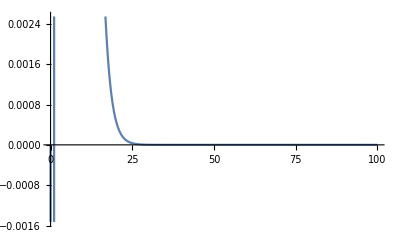

```mathematica
Plot[ef[[2]][r],{r,0,100}]
```

```mathematica
efr3[n_,r_?NumberQ]:=(ef[[n]][r])^2/r^3
```

```mathematica
NIntegrate[efr3[1,r],{r,0,2000.},MaxRecursion->14,WorkingPrecision->300,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity,Method->"LocalAdaptive"]
```

NIntegrate::ncvb: 在接近 {r} = {2.2006386959664490012317457275994410537312957947727643152837306567324351049465265795093947351782776332665829875080496520298281494126061595506783708102753045334611209178975024032673306564218521142449571416738980975125628937014620673479233370228868802305511057845937950126796607857759036782676750180068739049796819425542564312373791164406942632922317836×10^-308} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 20428.341920314867346465030206742490949485738571638356311707886403602796844757641226408318210654335501629417319332149813386299929228817735770338321617507383712277258613072327779446145368623708141415373383605628382572170885760063581176131522689230684906192181000959336720361459870131644884205773297896784532708129299052407778570431336278841894334236863 和 0.31171511338248636041515172658008579841139181973924127821426198815228225920397994018905876966344874489984479962127259276619370777487640387243926896389092248846644775989480512152897023547795530104652183213333807322931010857776019168011556320168933416939439480479205575540493647175398662345196618035384686934924795428108768869937248188879639329691978879.

NIntegrate::ncvb: 在接近 {r} = {3.1378418082652939707454048117758822000159895367861371807318034400571432238289133224040747330714291460089235259415482163017812496638249655171323754329520529838555441639220939756112322052804054516190595440559412878038934747032136484706032356232601930954634693395287123593305798812832538873635868677990373136662288534129729828372665640128006860131169916×10^-14} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7.8122158872175519963522827552764027961213801767621428411759663989515839631103833983866500126731905198198928783624141989706504846495523897003631186946061534671476297224873814405867065032564626627986467282674415248259407313021878122524319049513384263463025999135134750132641487293471652482938838297664736998229507960183656583814387391092501649431427253×10^-29 和 4.0288523964794555705484432706728952498758357381461372744718501826303128289677186271147089248410372480699656411691213061963898792807968942099972164476248362178393830206294598114498466191156244358062706344729997097911300775642545031058325886594605691677086483635669551643459945533920469260333537187200381562309546537749044022496968668746518702696072788×10^-47.

NIntegrate::ncvb: 在接近 {r} = {3.1378418082652941270107121808646304144008256808383870431804874888022558010540112966517859766981529802146147342618090669770167711355185289286282759696440027794456422361707591167944864971971174090993348927807201262097485090547280147821912779435320733862886847996440702214446794081855154597037662009249061132990739827651763436550862214958144706096986335×10^-14} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.9468994853532017494702106451822897022020666370366774187327909811632407840623422964950138646216478051237179713250389517125165518967756397441027539061150122279957073697490963050951053245432573192533922115175779199345824905459830875624305068871661333305003545424026968659023334960821767930181437558284482927015829827900220746046379102805170553887209915×10^-28 和 9.2323358235382717185555154437967663759863593994885190924642035809959480320016943959509810037090622964921890091282343880822895719349026997056184364712140546678925275835831188906291633050256119877508064393164298752121208259946549952792559887174155202006067228040721800449693715496536086938012050696334066804984702290916224455503050501362508570023227115×10^-47.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

```mathematica
NIntegrate[efr3[#,r],{r,0.,2000.},MaxRecursion->14,WorkingPrecision->300,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity]&/@{1,2,3,4,5,6}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 21319.226618325860584664379491202962516450153424020198580021481912017677158982721104965567582666079779545383181242270714624425911905687845992118093442333621402274550458782265593554731230405315710897714011468636407041426193292661076583538116590943267232809290293449029382248878623583478248141753906190920124277817832116046091965218296475749408979805991 和 20.03772434213127400572452472796386659906709659539891076538333717522486903135118279477705397932717781381446549248573687740058374867427592881574843137082647068573781161513046597454302885061639171634860159146381464997756096207519651076430198188695992230544793964973907331601951327108637361364033045477630554286629619542544275223852730910175086897241.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1368.9963509185007129276205977043731095853077592315550999592562059447525376264563940891252324420509437695467702311825136273849640918309917129646365226390832258035620832907028825727439238228688768641521040071307151900746096456484326177790588062839707445861466672663965203786875724916232013048523461170649368148768635311248171991885843621713816831598174 和 1.2867833563261827410936672996657872683882586320615792159066168570811842533520695814780279699400457364637911534437374337886799360157570185293816456176275958330493268880886638604918676242570652796452507797763308177659237883115042969847349848372000697253999770295078388231455155226440806690596006119166359663035189813644996292389314511586454824929345694.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

General::stop: 在本次计算中，NIntegrate::zeroregion 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 310.59229528463780108242122410768799749285158655909511316137843169744583751417211753884414602539523209102233419397762506984789329382595274305005190343687505962318381570867170730161920513407934074946644675248921433939783828993367271428324845729613133404797125838478148224329880233370655656370902228795183876167287555120907406426962432908611950521885004 和 0.2919426274425319311466133785175509006040392363679267874085009547273311024999741725914642104339801890251767358536783525359651831858239302473086656399663032815557940573173543726506233321381165340038436585833769747203481550432489208299445729298544943975558923054399330675164433964504379723856074017095364150423301664318571380658556695892763238199977164.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

{21319.2266183258605846643794912029625164501534240201985800214819120176771589827211049655675826660797795453831812422707146244259119056878459921180934423336214022745504587822655935547312304053157108977140114686364070414261932926610765835381165909432672328092902934490293822488786235834782481417539061909,1368.99635091850071292762059770437310958530775923155509995925620594475253762645639408912523244205094376954677023118251362738496409183099171296463652263908322580356208329070288257274392382286887686415210400713071519007460964564843261777905880628397074458614666726639652037868757249162320130485234611706,310.592295284637801082421224107687997492851586559095113161378431697445837514172117538844146025395232091022334193977625069847893293825952743050051903436875059623183815708671707301619205134079340749466446752489214339397838289933672714283248457296131334047971258384781482243298802333706556563709022287952,118.121621283675324697879752977619727577163306780594998766694158304675559186450082266804134932548720320665391485199058265016076017241771498730597010893966356171467154717497369299425480555207962866522805917894279817716278387918413972695604069226308837553787107828541961327410523097352293792754788959208,57.0661041548250219346801328131115806306686841874957592600364244751491351732824532165317834250906358637142245642551732362218822622457149482351704950543378619902239126657596486963451298888440036204650464504157233207571317855005060217052836214033827492862265180139519842772078005449226949656781871843147,31.8107264565207064455188001759029119058586189742971374595316130128466090279503797806597279130384501780349343491542155103018404229491826166763965154009140060847828666164702540466142866334068191873580567974534344015283598352868153539186924549739672895236433046356153143601144677258981262491804503532547}

```mathematica
NIntegrate[(ef[[4]][r])^2/r^3,{r,0,2000},Exclusions->{0},MaxRecursion->14,WorkingPrecision->200(*,AccuracyGoal->30,PrecisionGoal->30*)](*NIntegrate only worked when MaxRecursion is smaller than 15,which cause a considerable size of the estimated error.*)
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.511109902764844066023474353916813625254041281459353647982420404337659068566227890090370649675807936580936215338554322352477881190006309017778199766767283945591960214779234880447307589970698894574467383395098913884380014053323564400643736500050766781×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.115521299066440270969800807541515588732771902823010595260464970385823558591067824247985582567811513768767313248988013544648926561571418450232700586286400261523826784175669390667246807035542064883746581538334707129182631924244522853279804467619533499×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 118.202059780135744707805798564108504002469104945652406380841216336697036362623228184319215751147047547605728114977854836306455573988771040145627049614973351993753311440979001769253518126071194468278125494719830676195937815954229198496175952074556155 和 0.1690332676495628012379350439691336039196311216682397254128852408415960652986395130475848350167050884575482577210369493933049130721599009387404237455435626581810416316259198479967840704490568854213946368025464077488778375033306898043581258531228664256.

118.20205978013574470780579856410850400246910494565240638084121633669703636262322818431921575114704754760572811497785483630645557398877104014562704961497335199375331144097900176925351812607119446827813

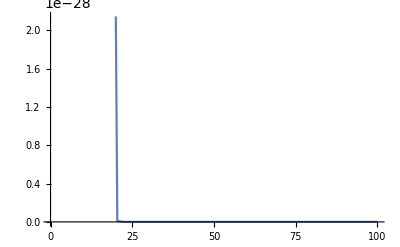
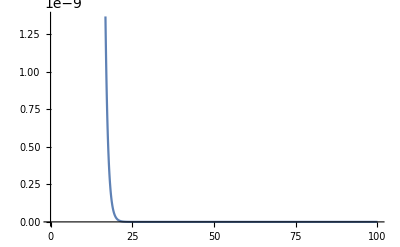
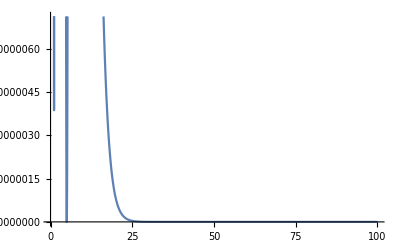
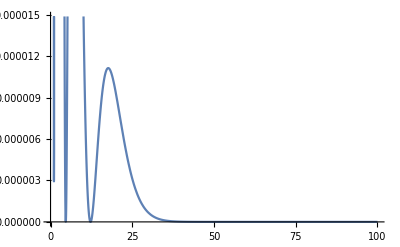
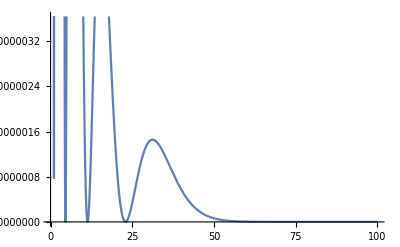
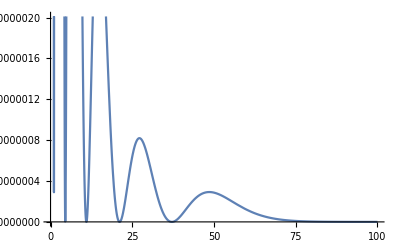

```mathematica
Plot[(ef[[#]][r])^2/r^3,{r,0,100}]&/@{1,2,3,4,5,6}
```

```mathematica
NIntegrate[(ef[[#]][r])^2/r^3,{r,0,2000},MaxRecursion->14,WorkingPrecision->300,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity]&/@{10,15,20}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.4783913043676297569284889744597787209937524818409208333293999262490433231268221026137801703880273003211255969728190200117082101335596340256519005234685506140465841717461447443315551133880969326177594012475329382187798262721193358531012042153124880884991279940132440047264063412868804702000411258358723757497779676735933463230976905366209561999848073×10^-220} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.3867028620446389858449677238191981092469401265104009438687094711687876394287221969291852205480932786834327376677925627936760769695690406609495893704021788145034076481347829583952489133579494221769382603164804007409473368250884545944571908045143806677727052485292305620380417431558197082060824985238174215920744219949442182801666574984132606444917343 和 0.017444243507801344993660053616538525237227590827497012921968449784132925644566557670774883080580637670171832981317430142860113070569617282203212233704791216251407063484566491346186650235780221049283559582400567928029964934606947167162842000610736746013823246064501737925259281777167026464764075803172043449229279526764447459167131053070413459234055009.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.8279401422284278404586672047314931196072631462666410937203614974495510826155485171442776236374916959194094001044362998581411526171551222776401750955848733929055062164238918452988445105662642045854946581848855821854828646970243541714300478364940800828326985375089436684957299976806216379775629225026287677733354376379664829893088677511128563268130722 和 0.0017181901652124861311026052715883792690908616092190027219233377307376718453288633697011662974437609092852717033054138997745504416008389308793514409324353973219711430638015595963520115873267023491478495721457888282224690437837546784653520759723522496083703547615608963442683361266200755531930853328876624859273675428668448039017804086852572429713345751.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

General::stop: 在本次计算中，NIntegrate::zeroregion 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.75783028884346936371193743882969840726950111996437230311360703914745204959822465764926829128481654725063057087875026169531118449363746986572488723812776876746280462001412291925015150782825417562749108478245282588243557226226670575058377435286056974741578477677945718317753547403870872801477105334561270817962999721985964990118848692782628917218865943 和 0.00071233013165915998054085326560278149977530791502638293275868703511254947880832877415561326399236391914986737824499308460843403902250171610601301232554867825323950595942815023474981718035116803412925668440160917455144642682097842138176260325941589923335462800985657278411248149872357237528527658306485882181507624403387109641814310609307897610313879426.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

{6.38670286204463898584496772381919810924694012651040094386870947116878763942872219692918522054809327868343273766779256279367607696956904066094958937040217881450340764813478295839524891335794942217693826031648040074094733682508845459445719080451438066777270524852923056203804174315581970820608249852382,1.82794014222842784045866720473149311960726314626664109372036149744955108261554851714427762363749169591940940010443629985814115261715512227764017509558487339290550621642389184529884451056626420458549465818488558218548286469702435417143004783649408008283269853750894366849572999768062163797756292250263,0.757830288843469363711937438829698407269501119964372303113607039147452049598224657649268291284816547250630570878750261695311184493637469865724887238127768767462804620014122919250151507828254175627491084782452825882435572262266705750583774352860569747415784776779457183177535474038708728014771053345613}

```mathematica
r3Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(efVs2[[n]][r])^2/r^3,{r,0,b},opt]+γ/a NIntegrate[(efVs2[[n]][r])^2 δa[r],{r,0,b},opt]+η a NIntegrate[(efVs2[[n]][r])^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
r3eva=r3Ture[#,2000][Z,γ,η,MaxRecursion->14,WorkingPrecision->300,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity]&/@{10,15,20}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.5965350824802117782245372320474711774217571835612470516267689463737614783836968701309839279368185520227939275003704660343361885658115694701548929154696796643455310381272967895703395583701928533966061896290242191635714946010542098053551945284207417854833680272410862796279023165181594796927271235983491362496622995182468347991259572756436599642817652 和 0.0014979703286564304976504954040467555823220657583820831012934226480366888621419425276458784588435440078816610053992145640045836231097371995795576058467111285909811649690852420450939608595476426062432601988031081486325334566151993537271975617969401148968479272982935252368767926181309546869353814869899512626417647233857230875526923918402092704137506217.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.92894666065099936290387464663682821087091832360772922536463906895286218303241204646817489981374237263588416549742599946476529959276898468609803878756184950115562429294272917369953694188984242850362025566366366102008631078358495062185538399830414471960825232761405948524921677938027869349944100466988466049633479000937405379404897838857565284893647311} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.000014480439392518343866215025305197644358989790441588386285449964455050758264114493205800893539528061106157160810773721376381502891509876314984003381262731578375525618394485221857326905932368297333268662091866423859731842183073174549758499389424571517328137497858867632594943269193377987023204552362104226933249075874164884194157999954950871788697755376 和 2.0871470030087168440010469721434060323518873190429546114705149690858590711648368368375862350680032994613817733189841510745747016918050884114991394500987993668223932209044697005075754277655746438261721851617793683637373659683434177690318703111426053378091769401076818429597055468751208220604923436354112007763998026707941904672365883546849410298130326×10^-18.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.92894666065099936290387464663682821087091832360772922536463906895286218303241204646817489981374237263588416549742599946476529959276898468609803878756184950115562429294272917369953694188984242850362025566366366102008631078358495062185538399830414471960825232761405948524921677938027869349944100466988466049633479000937405379404897838857565284893647311} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.000018715615775541577082331585708925785832734955938752048361388647548086165853775841726021844159561625149793427141719999124907321611150939909409888083167191342042439692609502453502710356257281689632457647424348425822850063822494714445720739122802330447090967464792989489266845188478790495773279035595736243516082007259863787747022071159831052781424355194 和 4.7045039055002792437840412844652733195165138769372761706281168000996699082723606185070333489800905008764839564810515120721207028271942081016764848000624621759288884311559495768430808865389457437153076320551311897735693642156806194480583031181663693737469682027812982031565020379586729566577004391683848968905363234852851807062738763080642626027408327×10^-18.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

General::stop: 在本次计算中，NIntegrate::zeroregion 的进一步输出将被抑制.

{1.59653508248021177822453723204747117742175718356124705162676894637376147838369687013098392793681855202279392750037046603433618856581156947015489291546967966434553103812729678957033955837019285339660618962902421916357149460105420980535519452842074178548336802724108627962790231651815947969272712359835 Z+0.0000144804393925183438662150253051976443589897904415883862854499644550507582641144932058008935395280611061571608107737213763815028915098763149840033812627315783755256183944852218573269059323682973332686620918664238597318421830731745497584993894245715173281374978588676325949432691933779870232045523621042 γ-0.0000187156157755415770823315857089257858327349559387520483613886475480861658537758417260218441595616251497934271417199991249073216111509399094098880831671913420424396926095024535027103562572816896324576474243484258228500638224947144457207391228023304470909674647929894892668451884787904957732790355957362 η,0.456526991985532252746502870375170703028079987734475497339042745018322643953224418151139781240988414523675513464868586341433065956326047157421520380671636882742151338128079986737590433033555320934047208650725576593470073812705066328911780270224177423770091220287173266370970687907913024757753237309241 Z+4.13621885375730371868486363198973572705933133565879716941161306002261997023859605437690686779327320682383478285867798093723695576982777603438091218471117987297091139596265477918791501281377226942326527793852556344942289738056823633927738822314100059618407503583200943207376622598073839069117808538759×10^-6 γ-5.3561155722173959040807230485947681355920279356274001090072045394291494842922440172356178789853043404238254400148326769439423387124049091962464922126474743068015978077163465048812261202917610851890596035222373092024992618330756998095556737000632884580633853056925711298070981796179682267136983923378×10^-6 η,0.189258504633002967460289084932075203796114714168461081041329394945504289121717057073408720979327361023716776634290995593385260293282921369453723921491260214791217622240685468127913833029873769845442719620817196010985149723697861364186127342236116526463441064503739249443819341305984541191209301623052 Z+1.71403604939225870383572666745469454112060822684080056206794356998854226256876926071543143400183862516669755788582868517447891811841204774074864053806492439968999933728485279900091697290685099709659413058772168092008640639973524890561849454491355400116558892141487787019847124260003481477557770662493×10^-6 γ-2.22098789213499478774678987209071356520028535131584856866429697574398292611951098653996117341775104177707001482536306913560988734386229026839032803603446847507024178959013638123047174498010949431140414402751665327937077061199932716519966686052894413037996874249793839098147572190726736233479378187601×10^-6 η}

```mathematica
FindRoot[Thread[r3eva==%65](*/.Z->1*),{{Z,1,5},{γ,1,3},{η,1,3}},AccuracyGoal->6,WorkingPrecision->300,StepMonitor:>Print@N[{Z,γ,η,r3eva-%65},6]]
```

{4.99885,49.275,-56.7504,{1.5959,0.454675,0.188454}}

{4.98718,516.612,-660.177,{1.59535,0.454516,0.188388}}

{4.85893,5655.73,-7295.82,{1.5892,0.452764,0.187662}}

{3.44818,62185.9,-80287.7,{1.52156,0.433493,0.179675}}

{-12.0701,684018.,-883199.,{0.777511,0.221514,0.0918133}}

{-28.2863,1.33382×10^6,-1.72222×10^6,{0.,0.,0.}}

{Z→-28.2862983014899024044264102237193450723484106653814601241126390364622545098030144246379937957315313654114901521819088170535638704777745193501421144426005147428575084705768271668896067498045445466709365926163068474750352115615109576616757804057017730847737405384909769811706374164939082121672880072567,γ→1.33381957508228754598627561088125655144741234294713486358075790010350617226601500949269465682958537727865627099203453654841938614308734630298756978089374727013322728390771085538813453827843146116369835212047863843020226833717936061105941770055295970860288763743843489755605030512657550353217501688495×10^6,η→-1.72222369399477278748248560923333265364094599297029094401774911493705878032404508332364123253202716678782915280323017005943488391115667206806827185457089913389204855301351626095779949410340324445737106969598068277752133992302270999642723345911794087240163480570578767936221335364531490246018473771074×10^6}

```mathematica
r3Ture[#,2000][Z,γ,η,MaxRecursion->14,WorkingPrecision->300,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity]&/@{1,2,3,4,5,6}/.%
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 2549.0028465028620038271010265827706079475928302773975831641734613705746484039001877722869194949727542995432061968007819506157529488970731079279463382972396495091202165477108089402277628240343534340846773371725072551784599151599528362868990343174027516394612787573971572448424599590130658053602509018182910421863239947314755435359683370199824254798508 和 2.3907607362028069320525573374231777069900516217037198533164771066059001964463763266420412370576587360729368216696280378308082470926911538736040657582786599324316083113287358057850690298868562238057317450332449479160821911159667009303261697803411107352196582486250539480138070724329384815567368989874268273778548531534736360263956801055836700485886618.

NIntegrate::ncvb: 在接近 {r} = {1.1496106815563687817299748819659802876513304928628957006510851971028980430967454111447749093544555156418806254164997226065997782445458307382703816729569085413659988577127634972110064647854112987476977648962172242051207160872872640497322243193498801395637028559806000372454505569476537110680521280676935922221852534543208240487252886451997051465235713} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.037931882660453578608331654437710800788282715821116398034509148048116654659347461169200245739431981540414846046459379789741660956488397474079404504088357009512332413171088334542995763692080910045819356444823732511216588483119027908071080113167726059242022625145519554543313940435188697062572176716511147064355378024274745804128781422433393890883743377 和 5.1452412460804104987611713260844535086417003572106072160167414920106320423073696573026428501966896148364102169364655533189528523300212278181661445189430955064074328529335747736350982287741959812978789758902940027621915147223080829110666067640975261341499783126235048721497107497978073876150682552513053089183564644551923633917080218972755256527170307×10^-14.

NIntegrate::ncvb: 在接近 {r} = {1.1496106815563687817299748819659802876513304928628957006510851971028980430967454111447749093544555156418806254164997226065997782445458307382703816729569085413659988577127634972110064647854112987476977648962172242051207160872872640497322243193498801395637028559806000372454505569476537110680521280676935922221852534543208240487252886451997051465235713} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.081864870686633850599030029966225668576597844181708558540592558323230344147720807996286084915284976932591417000896821659809472203524312273502457302519976896413492559773395441667197770853988702218534818902997289421957008583308678477665371398165510355089985036694091982047535972250233538962736745074890016155142916524529889836193882334346510300521860106 和 1.0617650167841801048663876075638420016643905984987832635133695692203658548924326399772128304082038346698696235606719396997146021289135525342758930824677369712343020087134797610495812298383246508661085060556090216081539125799149053325393291668616543979651180476868474039646107318864865853470994428001861135186049201256892715289139117128491486292444853×10^-13.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

General::stop: 在本次计算中，NIntegrate::zeroregion 的进一步输出将被抑制.

{119482.05272704949267878634550885722971787182308769033043246405667485627490094807999337906312274831874504476428871610094284184971358172843048941549638459969299472251224159755020329610939236260793581721351763754551174859929693140401519623698844569455199846828695661699933681306190140282850316963272913,1183.986342467043963292608622015533558481287333994851742869818782595412845280273109267608172788598438905496553996303959447413157459215929974836599095608451442789193058821506377989124916364403253809778019426512620722609754806659144949373134378168235492084109139386886323252100950857953917062348444813,302.8397114313315253619057776867956173423499723417872666617399707682404593361546909587526807482472410764553320566330228818595442051101983992368174832355907814425533302042843591565334086133932605157505017837994299060347621420398677816643111243072844908645172633667580745098958776018798799198265606947,116.9665400864722602119713572371402774289059139094473614868120740509782177880981925958190909495429111667504660146152948654377801413935403336071006351771212664022259361892786075209754170877802937944531474995613174324812498788724505051234044638072856699183557360313360550170166966606814999680634662007,56.20360390674867349303177534246159214380445443383889053624969041768915795762367490392179253238319206907566097353985984034593577847638618162208320127739498018375785249439104006112156200038428433981191508757503851749003088716554295606711403598509461811985856266589087145778798881412736434330016888251,31.85482504596160264369967952001466789404726206507859356091210729423058741594411717671263173824613759483828629268086266380775761615441248549565860956994356015425581780972167352178813219462216615559578844802438910689977792218927552896137057653437412447855820088143420276053983875597633360864024355775}

```mathematica
N[(%18-%%)/(%18),6]
```

{-4.60443,0.135143,0.0249606,0.00977874,0.0151141,-0.00138628}

{119482.,1183.99,302.84,116.967,56.2036,31.8548}

```mathematica
(%43-%)/(%43)
```

{-4.60443,0.135143,0.0249606,0.00977874,0.0151141,-0.00138628}

```mathematica
enVs2r3[n_?NumberQ,r_?NumberQ]:=(efVs2[[n]][r])^2/r^3
```

```mathematica
efVs2[[1]][0]
```

0.

```mathematica
NIntegrate[(efVs2[[3]][r])^2/r^3,{r,0.,2000.},MaxRecursion->14,WorkingPrecision->300(*,Method->"LocalAdaptive"*)(*,Method->{"SymbolicPreprocessing","OscillatorySelection"->True}*)]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 77.995529865622819285939356683628288958062911716052716443167451424239123987487815340090102738860477631150097258192345437533248396716920823111412220872889044625161563325776111279484410928462492927289896128331353105488097501135144074068809251449392065651930366033843758375628506940196046272565701935312309142633339492808978599763101919134796597119764745 和 0.073178857069046099064409254340903415354168977835784545412294590963148674840253537966560966637624251214668825047195928982547877142530158505587940650321947449111229916580900053253713626396336823477860505214639743509369741680189096004049858479791880947391373120868873411864874844026599051413525674006843373022087188843716366305633267078811244060939741153.

77.9955298656228192859393566836282889580629117160527164431674514242391239874878153400901027388604776311500972581923454375332483967169208231114122208728890446251615633257761112794844109284624929272898961283313531054880975011351440740688092514493920656519303660338437583756285069401960462725657019353123

```mathematica
NIntegrate[enVs2r3[#,r],{r,0.,2000.},MaxRecursion->14,WorkingPrecision->300,AccuracyGoal->30,PrecisionGoal->30,MaxPoints->Infinity]&/@{1,2,3,4,5,6}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 2549.0028465028620038271010265827706079475928302773975831641734613705746484039001877722869194949727542995432061968007819506157529488970731079279463382972396495091202165477108089402277628240343534340846773371725072551784599151599528362868990343174027516394612787573971572448424599590130658053602509018182910421863239947314755435359683370199824254798508 和 2.3907607362028069320525573374231777069900516217037198533164771066059001964463763266420412370576587360729368216696280378308082470926911538736040657582786599324316083113287358057850690298868562238057317450332449479160821911159667009303261697803411107352196582486250539480138070724329384815567368989874268273778548531534736360263956801055836700485886618.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 338.75106723093199851331167357658151451097254041108594327712660383903873629623090285889558141034034295523040897739735291785396549668889259926194159976952980447407150382603501354143364496991961541828439495824678056177031528805835988638331988809547739814044426407885791146641389813042198505719812898259747523772589659811547020898529876158982454265957512 和 0.31782082452998289920283093262164841628160155494615553564472580039538750855038283628364014390978066022255792387453864951622237384418394859213900092621076094994216595615332802159738707235334664098591056394444851157417378648699811274984323116216882953193959456275014998411653042837305329049986931991631902186071415920274355064329558863585702862970578394.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::zeroregion: 在指定的工作精度下，积分区域 {{0.,6.5111099027648440660234743539168136252540412814593536479824204043376590685662278900903706496758079365809362153385543223524778811900063090177781997667672839455919602147792348804473075899706988945744673833950989138843800140533235644006437365000507667809505137647456307154033574069174314472704876989263372660463744388553475611140342881907308657414492285×10^-443}} 无法进一步细分. NIntegrate 假定此处和任何进一步细分的区域都是零积分.

General::stop: 在本次计算中，NIntegrate::zeroregion 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.1232882189369655513769566560106818855501907743412371111312849791254851084124958837263669845981714325464715921076145895651480269496892938698921068996891006250891888397929929953041886749486496029926835734922186308126159860159406690569703655647927232547956386574731285973889632678976863877148624341341069438287210299318506682987825318053693310155564064×10^-294} 处的 r 中进行 14 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 77.995529865622819285939356683628288958062911716052716443167451424239123987487815340090102738860477631150097258192345437533248396716920823111412220872889044625161563325776111279484410928462492927289896128331353105488097501135144074068809251449392065651930366033843758375628506940196046272565701935312309142633339492808978599763101919134796597119764745 和 0.073178857069046099064409254340903415354168977835784545412294590963148674840253537966560966637624251214668825047195928982547877142530158505587940650321947449111229916580900053253713626396336823477860505214639743509369741680189096004049858479791880947391373120868873411864874844026599051413525674006843373022087188843716366305633267078811244060939741153.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

{2549.00284650286200382710102658277060794759283027739758316417346137057464840390018777228691949497275429954320619680078195061575294889707310792794633829723964950912021654771080894022776282403435343408467733717250725517845991515995283628689903431740275163946127875739715724484245995901306580536025090182,338.751067230931998513311673576581514510972540411085943277126603839038736296230902858895581410340342955230408977397352917853965496688892599261941599769529804474071503826035013541433644969919615418284394958246780561770315288058359886383319888095477398140444264078857911466413898130421985057198128982597,77.9955298656228192859393566836282889580629117160527164431674514242391239874878153400901027388604776311500972581923454375332483967169208231114122208728890446251615633257761112794844109284624929272898961283313531054880975011351440740688092514493920656519303660338437583756285069401960462725657019353123,29.5949834052195923344509361042965890982150690956622855818939740348562962079817913602829698783440796337365579146762827247426066005320720105846854039240520056137604713439383160430219761762237488488650280605173278200531575728593568522132781264855812921939246920076353379481963092827189574688446412015425,14.3000901990615152024064620192953650151656267251260505021369485238217021468322069254557549214132446041598500347811249311772294365207672436995375450065601541569683943525060327929859369083880416634238085013408199186794288712084298194509282552473188467767621193237950786194998487029123272898303100750876,7.94969424514729872380588688912818857540007213755225850377570383690677610329881685401677837844104748684792493104663645588757309126446866429261514914433586147878199237545532913532024553108748750562028676947685138886929217290338728446711466320153233909350446258255255238654231840837617257970125594575283}

```mathematica
N[(%18-%61)/(%18),6]
```

{0.880436,0.752555,0.748881,0.749453,0.749412,0.750094}